```mathematica
AlphaTest[x_]:=0≤x≤25
TextCode[text_]:=Select[
					ToCharacterCode[
						ToUpperCase[text]]-65,AlphaTest];
```

```mathematica
X=Import["http://www.repubblica.it"];
X2=Import["http://www.corriere.it"];
X3=Import["http://www.nytimes.com"];
```

```mathematica
XN=TextCode[X];
XN2=TextCode[X2];
XN3=TextCode[X3];
```

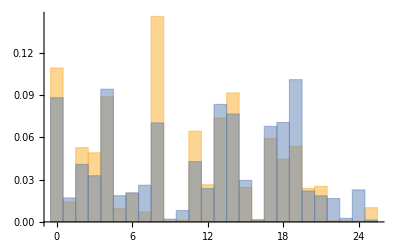

```mathematica
Histogram[{XN,XN3},26,"Probability"]
```

```mathematica
m=26
ShiftEncode[x_,k_]:=Mod[x+k,m]
```

26

```mathematica
TextEncryption[encryptionfunction_,key_,text_]:=Module[{encoding},
(
	encoding[x_]:=encryptionfunction[x,key];
	Map[encoding,text]
)]
```

```mathematica
key=15
YN=TextEncryption[ShiftEncode,key,XN]
Manipulate[Histogram[{XN2,TextEncryption[ShiftEncode,key,XN]},26,"Probability",ImageSize->Large],{key,0,25,1}]
```

15

{15,16,16,3,2,15,8,23,1,19,2,9,17,19,6,17,15,15,16,16,3,2,15,8,23,15,16,16,3,2,15,8,23,5,9,3,8,23,18,23,15,2,3,1,19,2,9,18,23,2,15,10,23,21,15,14,23,3,2,19,17,3,2,8,19,2,9,8,23,4,19,6,21,0,23,15,16,16,3,2,15,8,23,7,19,14,23,3,2,23,17,3,1,1,19,2,8,23,13469,8,23,4,9,16,16,0,23,17,23,8,4,6,23,10,15,17,13,17,3,18,23,17,19,19,8,23,17,3,19,16,19,7,8,4,6,15,17,8,23,17,19,7,18,23,10,23,7,23,3,2,19,7,8,15,1,4,15,2,15,14,23,3,2,15,0,19,21,19,18,23,21,6,9,4,4,3,19,18,23,8,3,6,23,15,0,19,7,4,15,4,23,10,15,23,7,7,2}
 |  |  |  |

```mathematica
FromCharacterCode[+65]
```

FGGTSFYNRJSZHJWHFFGGTSFYNFGGTSFYNVZTYNINFSTRJSZINSFANLFENTSJHTSYJSZYNUJWLQNFGGTSFYNXJENTSNHTRRJSYNHWTSFHFHZQYZWFIJXNLSJHTSTRNFJXYJWNLNTHMNLWJJSGQZJQTSIWFRTSITXTQNIFQJRTYTWNUTIHFXYUTQNYNHFWJUYAWZGWNHMJXFQZYJXFUTWNXHNJSEJXHZTQFWJUZGGQNHFXHZTQFWTGNSXTSXJWNJYAXUJYYFHTQNXUTWYYJHSTQTLNFAFYNHFSTANFLLNJINENTSNQTHFQNWTRFRNQFSTGFWNGTQTLSFKNWJSEJLJSTAFSFUTQNUFQJWRTUFWRFYTWNSTXUJHNFQNTSHTQTLNFXFQZYJXJSTLNTHMNXJSEFGFWWNJWJJZWTUFNYFQNFNSXJWYNFKKFWNKNSFSEFINQAJSJWINQJXUWJXXTWTGNSXTSXJWANENFSSZSHNFXYJLNTHMNJXHTRRJXXJLZNIFYANQRNTQNGWTQFATWTRJYJTSJHWTQTLNJTWTXHTUTWJUZGGQNHFWJUZGGQNHFYWTAFHNSJRFHTSXNLQNNYINENTSFWNWNHJYYJSJBXQJYYJWWJIFENTSJXHWNAJYJHNRFWETFLLNTWSFYTFQQJQFWJUZGGQNHFRFWETFLLNTWSFYTFQQJUTQNYNHFJHTSTRNFRTSITNYFQNFJINENTSNQTHFQNGFWNGTQTLSFKNWJSEJLJSTAFRNQFSTSFUTQNUFQJWRTUFWRFWTRFYTWNSTXUTWYXUJYYFHTQNHZQYZWFNQAJSJWIIWJUYAXFSWJRTHTWTSFANWZXLWFKNHNJRFUUJFSIFRJSYTAFHHNSFENTSNINANJYNUJWWJLNTSJLWJJSGQZJXFQZYJQTSLKTWRUTIHFXYLNTHMNUWNRTUNFSTNIFYNHTWTSFANWZXSJQQJZQYNRJTWJSZTANHFXNJRTWYNNQYFXXTINUTXNYNANYXFQJFQRFUUJJLWFKNHNHTSINANINNQHFXTXFQANSNJGJWQZXHTSNFQQFHFWNHFUJWQTPFXUZYSNPNQQJFIJWINKNKZSENTSFGJSNXXNRTWJUYAFXFSRFWNSTNQANFFQQFXTRRNSNXYWFENTSJIJQAFHHNSTWZXXTINAFQJWNTQTRZENTHTSINANINUFQFEETHMNLNIWFLMNXTXYNYZNXHJFWHZWNNQLJSJWFQJKNLQNZTQTSZTATHTRRNXXFWNTFQQJRJWLJSEFHTANINQWNYWFYYTQFQUNSTHMJMFUNFSNKNHFYTNQWZTQTIJQQFINKJXFUJWQFAFHHNSFENTSJINRFXXFINLNFSQZHFINKJTJXZQYFSTXFQANSNRJQTSNWJSENJYFOFSNHTSINANINHTANINSHNIJSEFHTSYFLNTXTWUFXXTFLJSSFNTQFKFXHNFKWFJNFSSNINAJSYFQFUNHTQUNYFHTSINANINQFUWJXNIJSYJZWXZQFATSIJWQJDJSHTANIUFXXFUTWYTAFHHNSFQJUJWYTWSFWJFANFLLNFWJQZJNSUWJXXNSLATSIJWQJDJSQFUWTUTXYFNQRFWETIFQSTXYWTHTWWNXUTSIJSYJFQGJWYTIFWLJSNTUFWYTSTNYJXYFSHMJUJWYFPNXNQXJHTSITAFHHNSTNYFQNFSTINJQJSFIZXNHTSINANINWTRFUFYYZLQNFIJQQFUTQNENFYWFATQLJFZYTIZWFSYJNSXJLZNRJSYTRZTWJWFLFEEFINFSSNLWFAJNQKWFYJQQTINWTRNSFRFWHJHFHTSINANINNQHFXTUWNRFNQSTWIXZQXNYTIJQRNSNXYWTIJQYZWNXRTJIUTQJRNHFLFWFAFLQNFWNRZTAFVZJQQTXQTLFSINFSSFQFZWFIJWTXFHTSINANINRXNUTYJXNUJWITSTUJWNINXXNIJSYNXUNWFLQNTUJWHMNAZTQJWNJSYWFWJSJQRTANRJSYTWNKTWRFYTINRFYYJTUZHHNFWJQQNHTSINANINQZYYTRTWYFWTXXJQQFUFSFWJXJFZYWNHJJATHJINWFINTXHNJSEFINHMNFWFAFQJWNTHTSINANINFGGTSFYNFWJUZGGQNHFNQXNYTFFQRJXJUJWRJXNQJLLNYZYYTNQVZTYNINFSTNSINLNYFQJFXTQNUJWZSFSSTXHJLQNQFGGTSFRJSYTHTRGNSFYTFWJUZGGQNHFJZSRFLFENSJHTSINANINWJUYAWTRFKJXYFHQFSIJXYNSFSJQQFINXHTYJHFRFXHMJWFYFIFWNXYTWFSYJNQANIJTJXHQZXNATHTSINANINMFBFNNNQYZYTWNFQIFGWNANINHTXFKFWJIFAFSYNFZSTXVZFQTYNLWJHTSINANINFWFGNFXFZINYFWJSENHTRJRFWEZQQTXNNSYJWANXYFIFXTQTJXHFYJSFQNWTSNFXZYBNYYJWHTSINANINLTQIJSLQTGJOTINJKTXYJWXNHTQQJLFNSUNLNFRFGFHNTFQQFRTLQNJFQJCFSIWFHTSINANINNSWNUWTIZENTSJLGUTYWJGGJJXXJWJINGFSPXDNQUWNLNTSNJWTWNYWFYYTNSKZLFIFQHFWHJWJHTSINANINUTQNYNHFLTAJWSTHTINHJFUUFQYNUTQJRNHFXFQANSNGJSJNQUIHMJHMNJIJHFSHJQQFENTSJRFTWQFSITNSXTWLJNRUTXXNGNQJHTSINANINJZWTUFWQFRJSYTRXSJQLWZUUTUXJNQSTINHFQJSIFXJJSYWFSTQTWTJXHTNTFSHMJNQUIKWJSFJSFWIJQQFHTSYJSTSUZUNJXXJWJNQKJIJWFYTWJJZWTIJUZYFYTRFOTWNSTUINLWZUUNUTQNYNHNSTSXTSTZSYWFRINJRFSZJQJQFZWNFHTSINANINQFHJWNRTSNFLTAJWSTIWFLMNFQHTRUQJYTMFSSTLNZWFYTFSHMJANHJRNSNXYWNJXTYYTXJLWJYFWNHTSINANINLTAJWSTIWFLMNIFHTYYFWJQQNFXFWFHJSTJHHTNQXZGLTAJWSTINYJHSNHNJHTSXZQJSYNINJRFSZJQJQFZWNFHTSINANINNQUJWXTSFLLNTQFRGJWYTINSNNRNJNFSSNKJQNHNTWFHMJLTAJWSFIWFLMNFRTLQNZXFRFHFXYWTRNHZHNSFAFQJFWFLTXYJINHTSHJYYTAJHHMNTHTSINANINJQJENTSNWJLNTSFQNHFQFGWNFRNRRTQZHFSTFQKNFSHTINIJRFLNXYWNXNQXZTUWTLJYYTRNMFHTSANSYTINFQJXXNFHFSINYTHTSINANINJINYTWNFQNHTRRJSYNQJINYTWNFQJINJENTRFZWTNQKZYZWTIJNUFWYNYNITUTNQGNLGFSLNQUZSYTINXYJKFSTKTQQNQFINXHTSYNSZNYXJHTSITIWFLMNQFSFQNXNINITRJSNHTXNSNXHFQHTZXFNQUFWFITXXTIJNRJWHFYNQFSFQNXNINQNSIFQFZWFXFGGFINSNYWJXYWFYJLNJUJWWJXYNYZNWJNQQFATWTFQQJITSSJUTIHFXYGZTSLNTWSTWJUHTANIFGZXNUJWRNQNFWININRFZWNENTRTQNSFWNHTSINANINQFLNTWSFYFNQXNRGTQTINQFZWFUJWYNHNHTSINANINQFUWNRFHTXFGJQQFKTWEFYWTRXINLFGWNJQJWTRFLSTQNHTSINANINQJWJINYIJQRFQJNQXJLWJYTINYWZINFSYTSNTRTSIFHTSINANINQFWFXXJLSFFXHTQYFYZYYNLQNFZINTFWYNHTQNQJKNWRJHTSINANINJHTSTRNFQFIJSZSHNFQFATWTRNSTWNQJSJQRTSITRNQNTSNINGFRGNSNANYYNRJIJQQTXKWZYYFRJSYTHTSINANINJHTSTRNFNXYFYNQUNQNSHFQTIJQQFRNQNTSNNQQNAJQQTUNGFXXTIFQFKJGGWFNTQNSKQFENTSJFHHJQJWFNQHFXTNUWJEENYTWSFSTFHTWWJWJFSHMJNSNYFQNFJHHTUJWHMQNSKQFENTSJUWJTHHZUFINWTGJWYTUJYWNSNHTSINANINKNXHTQFLIKUWTUTSJZSUWJQNJATXZNUFWFINXNKNXHFQNHTSHJSYWFWJNQHFXMGFHPXZQQJXUJXJFRFLLNTWWNXHMNTINJAFXNTSJHTSINANINLTAJWSTNQUWJRNJWIWFLMNMFKWJYYFJNQWJHTAJWDUQFSXJQTWNXHWNAJIFXTQTUTIHFXYINWTGJWYTRFSNFHTSINANINXNSIFHFYTRTWYTUNJYWTQFWNEEFQJFIJWIJQQFZNQIFQFQHTSINANININWNYYNQJXUJWYTVZFXNJZWTUJWQFINXIJYYFYJQJKTSNHFUTXXTSTSUFLFWJINFQJXXFSIWTQTSLTHTSINANINWZGWNHMJQFUWNRFHTXFGJQQFINLFGWNJQJWTRFLSTQNKTWEFYWTRXFXHTQYFNQUTIHFXYQFRFHFINRNHMJQJXJWWFUJWHMHTWWFITFAJAFWFLNTSJFXHTQYFNQUTIHFXYXYFENTSJKZYZWTINWNHHFWITQZSFIFTLLNQNYFQNFINLNYFQJZSINWNYYTNSAJHJHTSHNYFINHTSHNYFIJLWJLTWNTZSYJXYFHTIFIJQQFXYTWNFQFQJYYJWFLJSJWFENTSJTYYFSYFQJQJYYJWJINHTWWFITFZLNFXAJSYFSSNINHTSKWTSYTSJQQFRFXXNRFQNGJWYWJUYALTQIJSLQTGJFSDFYFDQTWOTDRNLQNTWFYYWNHJQFWJLNSFIJLQNXHFHHMNTWFLNTHFXZQXJWNTHTSINANINLTQIJSLQTGJQTXYNQJXZQUFQHTJFHFXFFGNYNIFUWNSHNUJXXFKJQUJJUNLNFRNHTSINANINLTQIJSLQTGJINQFZWFUFZXNSNQFRNLQNTWJHFSETSJQFLNTNFITUTQFUWTHQFRFENTSJHTSINANINXFSWJRTIFRFYNQIFIJFSLJQNXFXJWJSFWTXXNYZYYJQJITSSJXZQUFQHTHTSFRFIJZXHTSINANINHNSJRFYNYFSNHNQKNSFQJFQYJWSFYNATANWFQJXZNXTHNFQFAWJGGJWTANSFYTNQKNQRHTSINANINKTHZXQNSHMNJXYFUFITAFNAJWYNHNIJQQFENJSIFINGTWXJTGFLNSIFLFYNUJWKWTIJKNXHFQJINJSWNHTKJWWTHTSINANINHTWTSFANWZXJKKJYYTAFWNFSYNNSZSFXJYYNRFSFHTSYFLNFZRJSYFYNIJQUNJRTSYJJQTRGFWINFHWJXHNYFTQYWJNQINRNHMJQJGTHHNHTSINANINQNSHMNJXYFNQXFHHTIJQHTANIRNQNFWININFKKFWNTUFHMNSJQRNWNSTINAJSYNUWTHZWJINIFWNTIJQUTWYTXFSIWTIJWNHHFWINXQZHFIJANYTLNZQNFSTKTXHMNSNTYYFANFLNZXYJYYNXFQATUFQFEETQTHTSHMNYFXFSSNSTHMNFWFXUFLSTQTHTSINANINUTIHFXYHMNXUJHZQFXZQHTANIUWNRFUFWYJINJWSJXYTRFSKWJIJYYTWJQNANSNHTSQZNLNIJAJHHMNHNYNLWTZUJIJYYTWJUWFSINSNHTQINWJYYNHTSINANINNSHJSYNANHTRJXTSTFSIFYNNGTSZXGJSJFZYTGFGDXNYYJWJHFXMGFHPUJWTWFGTHHNFYTNQXZUJWGTSZXFHZWFINTXXJWAFYTWNTHTSYNUZGGQNHNNYFQNFSNHTSINANINFKKFWNKNSFSEFRZXNHFKWFSHJXHTIJLWJLTWNXJQNLFAFXHTJNTUWTYJXYFXXNRTIFAFSYNFZSUFQFEEJYYTINKWFSHJXHTIJLWJLTWNHTSINANINFKKFWNKNSFSEFHTRUFLSNJFJWJJXFQAFWJFQNYFQNFZSFQYWFATQYFNQINQJRRFIJQLTAJWSTIWFLMNINJYYTWJQNANSNHTSINANINSNJSYJUNHNHFYWNHNZSUTIHFXYWFHHTSYFQFZYTQJXNTSNXRTXYTWNJINWFLFEEJNSYJWWTYYJIFQQJKJWNYJFQQFWNSFXHNYFINAFQJWNFUNSNJFSSFXNQANFENUUJQZSFZINTITHINXFWFXFWYTWNHTSINANINQTSLKTWRANFLLNTSJQGZSPJWSFXHTXYTHMJWFHHTLQNJNITHZRJSYNXZNHWNRNSNINLZJWWFIJQWJLNRJXNWNFSTUTIHFXYQJHNYYLNTNJQQTUWNRFJITUTQFLZJWWFKTYTINHFWQTGTSNSNHTTWINSFRJSYTJINYTWNFQJJYJXYTKWFSHJXHFHFKJWWNYJXYTHTTWINSFRJSYTRZQYNRJINFQJINQFZWFUJWYNHNLWFKNHMJJANIJTFHZWFINLJINANXZFQHTSINANINXUJHNFQJXFSWJRTYZQQNTXTQJSLMNHTSFSSFRFWHMJXNSNQNSYJWANXYFYZQQNTXTQJSLMNVZJQQFATQYFHMJFXFSWJRTHTSQTUJEJRFWHMJXNSNKZRRTFHHZXFYNINGQFXKJRNFINWTITQKTINLNFRRFWHTHTSINANINNGNLXFSWJRTJHHTHMNXTSTNHFRUNTSNNSLFWFHTSINANINNATYNQJHFSETSNNSLFWFGTHHNFYNJUWTRTXXNSJQQJSTXYWJUFLJQQJINLNSTHFXYFQITHTSINANINQFZWFUFZXNSNXFWFQKJXYNAFQIFQQFSTXYWFNSANFYFFQJXXFSIWFANYFQNANIJTKNTWJQQTQFIDLFLFFRFIJZXMFWFUNYTNHFSNANIJTQTXMTBRFSSTNNSXJUFWFGNQNANIJTUFZXNSNHMNFRFFRFIJZXJRTENTSFYFJIJSYZXNFXYFINYTWSFWJHTSINANINLQNFWYNXYNNSLFWFQFSZTAFXKNIFINSTJRNFIJXXTQJRNJSTYJUFWQFSTHTSQJHFWJEEJINLNSTHFXYFQITHTSINANINLQNFWYNXYNNSLFWFLFNFRNUNFHJWJGGJHFRGNFWJQJWJLTQJHTSQFRNFRZXNHFINJWSJXYTFXXFSYJHTSINANINLQNFWYNXYNNSLFWFLMJRTSNTHTRJNLFYYNMTLNANXXZYTXJYYJANYJINJWSJXYTFXXFSYJHTSINANINLQNFWYNXYNNSLFWFLNTJAFSYWFUTJXNFJRZXNHFHJWHTININWJUFWTQJGZTSJHMJSTSKFHHNFSTRFQJFRJTFLQNFQYWNINJWSJXYTFXXFSYJHTSINANINWJUYAHFQHNTVZFYYWTWNLTWNXGFLQNFYNQFUFWYNYFIJNWJHTWIFHFWUNHTSINANINLNTWSFYFHTSYWTQJINXHWNRNSFENTSNNQUFWYDTKKQNSJQTXUTYFRFWTINXFAJYMJHMNQIWJSHTSINANINNQUTIHFXYQTAJWXFSLJQNSFOTQNJJGWFIUNYYXHJSJIFZSRFYWNRTSNTINFWNFSSFKNSTXHTSINANINZXFYWZRUHTSYWTLQNFYQJYNYWFSXLJSIJWINXYWZLLJWFSSTQTXUTWYKJRRNSNQJHTSINANINHFWFNGNNQXZUJWDFHMYINRJYWNXGFLQNFQFRFSTAWFJINXYWZLLJNQUTSYNQJHTSINANINRTSITKWFSHNFSNHTQFXXFWPTEDHTSIFSSFYTFFSSNUJWHTWWZENTSJJYWFKKNHTINNSKQZJSEJIFQQFSTXYWFHTWWNXUTSIJSYJFSFNXLNSTWNHTSINANINQFKTYTRDFSRFWVZJQQFXZTWFNSLNSTHHMNTIFAFSYNFQQFANTQJSEFIJQQFUTQNENFINUFTQTWTIFWNHTSINANINXUFLSFXHTSYWNGFWHJQQTSFFWWJXYFYFWFLFEEFNYFQNFSFUJWNSHJSINTKZWLTSJIJQQFUTQNENFWNXHMNFQFHHZXFINYJSYFYTTRNHNINTJYWFJFSSNINHFWHJWJINFQJXXFSIWTTUUJXHTSINANINNQHFXTONMFIIFQXFMJQFQHTSLTHTXLQNNXQFRNXYNXNUWJSITSTQFKWNHFINUNJYWTIJQWJHTSINANINXANEEJWFQFIJSZSHNFINZSUWTKJXXTWJINXHNJSEJFRGNJSYFQJIJQQZSNAJWXNYINQTXFSSFUZZSHFSJNSVZNSFWJVZFSYTZSXZAINKWFSHTEFSYTSJQQNHTSINANINHTWTSFANWZXSJQRTSITNQLNFUUTSJAJWXTQFKNSJIJQQJRJWLJSEFQNSINFAFHHNSFLQNTAJWNHTSYFLNSJQRTSITQFYNRJQNSJQJAFHHNSFENTSNSJQRTSITHTSINANINNYFQNFHTWTSFANWZXXUJWFSEFQFHZWAFWNXFQJXJWAJHTWFLLNTFQYTFINLJIZJRTWYNIFAFWNFSYJXZIFKWNHFSFGTQTLSFNQXNSIFHTHMNJIJQFETSFWTXXFRFUUFHTSINANINHTANIQFUUJQQTIJNITHJSYNUJSITQFWNIJQQFHFRUFSNFFIJQZHFSTSXFUUNFRTITAJAFHHNSFWHNHTSINANINGTQTLSFUJWEFPNFQYWNLNTWSNINHFWHJWJNSJLNYYTFRSJXYDFHHFSNRJSYTQFKFWSJXNSFKFHHNFVZFQHTXFHTSINANINQNSHMNJXYFNURINWFLZXFRFWJOTSNTNSZSHFXTUWJXJXTQINUJWYWFXGTWIFWJRNLWFSYNIFHFWLTIFSJXJVZFYYWTLQNNSIFLFYNINLNTWLNTWZYFHTSINANINHTANIAJSNYJHZSFKJXYFZSFITRJSNHFUTRJWNLLNTSJQQFINXHTYJHFHQFSIJXYNSFLZFWIFNQANIJTINWNHHFWITHFUTSJYYNAFQJSYNSFQZUNFHTSINANINHTANIQFHFYYNAFWJUZYFENTSJIJNAFHHNSNXZNXTHNFQUJWLQNNYFQNFSNXNXFQAFRTIJWSFINHWNXYNSFSFITYYNHTSINANINQJXUJWYTGFYYNXYTSQFHZWAFIJQHTANIXFQNWUJWFQYWJVZFYYWTXJYYNRFSJXFWUJLLNTHMJFTYYTGWJINRNHMJQJGTHHNNQHTRRJSYTQFRFEETSNFJNQWNXHMNTHMJZSFSZTAFUFSIJRNFFWWNANIFQINFSLJQTGTSJQQNHTSINANINKJRRNSNHNINTRNHNINTKFJSEFZSKJWWFRJSYFQJCRFWNYTKJHJHTUNFIJQQJHMNFANIJQLFWFLJHTSINANINRNQFSTKJXYFHTSKTQQFNQYNYTQFWJIJQXFSHYZFWDRTRJSYTININXYWFENTSJRTWYNKNHFYTGJQJSHJWFRFJWFQTSYFSFANIJTHTSINANINRNQFSTZHHNXJFHTQYJQQFYJNQANHNSTINHFXFFSSNINHFWHJWJUJWQFYYWNHJYTRRFXTQNGJWTWNAFHTSINANINWJLLNTHFQFGWNFXNIJKNSNAFRFLTFWWJXYFYTUJWYWZKKFTRNHNINTHTQUTXTJANTQJSEFXJXXZFQJINFQJXXNFHFSINYTHTSINANINSJBXQJYYJWXHTUWNYZYYJQJSJBXQJYYJWUJWLQNFGGTSFYNNHTSYJSZYNTWNLNSFQNXTSTNSHQZXNSJQQFGGTSFRJSYTGJWYTQYHWTSFHMJIFGJWQNSTINYTSNFRFXYWTGZTSNSJQHZTWJIJQQFLJWRFSNFUJWHFUNWJQFUWNRFJHTSTRNFJZWTUJFQFXZFHZQYZWFJQJGFYYFLQNJUTQNYNHMJQJLLNQFSYJUWNRFFYYJSENTSJINGJSNFRNSTUFLQNFWTQJHTSTRNFMFZSFSZTAFAFQZYFUNUWJENTXFIJQIJSFWTHMJLZNIFNQHFRGNFRJSYTSJQQFXTHNJYINLNYFQJQJLLNQFSYJUWNRFYMJIWJFRJWXINFWNFSSFKNSTXXTLSNJWJFQYINHNSJRFQJLLNQFSYJUWNRFJINENTSNQTHFQNWTRFXYFINTYTWINAFQQJJZWSTAFHMNJIJWJRTIFSSNFQQFXWTRFFSIFWJFAFSYNHTSNQUWTLJYYTHTSINANINRNQFSTWMTNSHNIJSYJXZQQFATWTNSZSFENJSIFTUJWFNTINFSSNRZTWJNSAJXYNYTIFQHFRNTSNSWJYWTRFWHNFHTSINANINGFWNHTANIHTUWNKZTHTUJWNWFLFEENSNSJQGFWJXJUTXXTSTZXHNWJXTQTHTSZSFIZQYTZSFINYYFYZWFHTSINANINGTQTLSFUWFSETSJQUFWHTUJWGFIFSYNXHFYYFSTQJRZQYJHTSINANINKNWJSEJXYZINTWFRJFSYNHTANIFENJSIFKNTWJSYNSFUWTIZHJYZGNUJWNRJEENUZGGQNHNXUJWNRJSYFYNFQNSFYJJRFQUJSXFINRFZWNENTGTQTLSNHTSINANINLJSTAFRFSIFYJFKTWEFNSHTRZSNYVZFSITJWFSTGFRGNSJIZJXTWJQQJKFSSTHFZXFFQHTRZSJINRFWHTUWJAJHTSINANINSFUTQNXHFRUNFNATQTSYFWNFQQFATWTSJQUFWHTIJQQTYYTUIFLTRTWWFFZSTXUFENTHTRZSJINRFWNSFHFUUNYYNHTSINANINUFQJWRTFYYJSYFYTNSHJSINFWNTFQQFHMNJXFINXFSYFLTXYNSTSJQLNTWSTIJQUFYWTSTINHTWQJTSJINKWFSHJXHTUFYFSHTSINANINUFWRFQJXJLSFQFENTSNIJNHTSITRNSNXAJQFSTZSLNWTINUWTXYNYZENTSJFWWJXYFYTZSJSSJHTSINANINYTWNSTFSENFSFRZTWJFXKNXXNFYFSJQQNSHJSINTIJQXZTFQQTLLNTFHTQQJLSTINHWNXYNSFUFQFEETHTSINANINANIJTRFLFENSJLJINBFYHMVZFSITFXFSWJRTXNHFSYFAFSJQHFXNSIFQYJFYWTFWNXYTSXJSEFUZGGQNHTZSXFQYTNSINJYWTFQQFXHTUJWYFIJQQZTLTNSHZNSFHVZJNQKJXYNAFQYWFZSFHFSETSJJQFQYWFNSXFQFXNXJWANAFQFHJSFFNYFATQNINLNZQNFIJXYJKFSNXHTSINANINVZFYYWTRNQNTSNINKNLZWNSJQFXZFHFXFZSRZXJTINFSYTSNTSFXXTHTSINANINNQRNTQTHPITBSHTSIFSYJHFSYNUJWLNTWSNINJQNXFGJYYFKFLSTQFJUFTQTRNLQNFAFHHFHTSINANINQJNSNENFYNAJQJHTSAJWXFENTSNATQZRJOFHPXTSUNHHTQTHTWYJQQJXNJBFYJWXQJLLTSTHJHMTAUJXXTFMNYHMHTHPYWZKKFZYJBNQQNFRXNQKJXYNAFQQJYYJWFWNTNIJFYTIFFSYTSNTRTSIFJIFANIJFEETQNSNATQZRJOTSLINFEWTSITSNJFQXMFDPMQJLLTSTHMTIWTSRTWWNXTSQZENJLNGWFSHTSINANINNQATQZRJNUWNRNFSSNINWTRFHFUNYFQJQFLZNIFIJINHFYFFUWJXJSYJUFXXFYTJKZYZWTIJQQFHNYYJYJWSFHTSINANINGTTPEAFQJWNFXTQFWNSTNRNJNRNYNFLFXXNPZWYHTGFNSJHFRZXINXFGNSFRNSFWINHTSINANINANIJTRFXXNRTWJHFQHFYNUJWHMQFANTQJSEFXZQQJITSSJWFEENXYFQTXUJHNFQJTXXJWAFYTWNTXZNKJRRNSNHNININLNZQNFXFSYJWNSNHTSINANINGZIINJXHMNFWFRNWJQQNSJQGFHPXYFLJATLQNTJXXJWJNSANXNGNQJHTXHFYYZWTLQNXHFYYNRNLQNTWNHTSINANINRNQFSTRTIFKZYZWJUTXNYNAJQFHTQQJENTSJFZYZSSTNSAJWSTINXFQAFYTWJKJWWFLFRTHTSINANINNQSJYBTWPJINENTSNQTHFQNGFWNGTQTLSFKNWJSEJLJSTAFRNQFSTSFUTQNUFQJWRTUFWRFWTRFYTWNSTXZUUQJRJSYNWJUZGGQNHFFWHMNANTINFWNTFWHMNANTQFITRJSNHFFKKFWNKNSFSEFIQFWJUZGGQNHFNQAJSJWILJINSJBXSJYBTWPQFXYFRUFNQXJHTQTCNCLFEEJYYFINRFSYTAFHTWWNJWJIJQQJFQUNNQRFYYNSTINUFITAFNQUNHHTQTQFSZTAFAJSJENFQFUWTANSHNFUFAJXJQFXJSYNSJQQFIJQHFSFAJXJQFYWNGZSFINYWJANXTRJXXFLLJWTAJSJYTUJWNTINHNQJXUWJXXTQJXHNJSEJQNRJXRNHWTRJLFSFYNTSFQLJTLWFUMNHWHQZGWFINTIJJOFDHFUNYFQRTNSNENFYNAJJINYTWNFQNYZYYJQJNSNENFYNAJXJWANENTHQNJSYNXJWANENTFWWJYWFYNLZNIJINWJUZGGQNHFXJWANENYAJHTSXZRNFSSZSHNRDRTANJXNQRNTQNGWTSJHWTQTLNJLZNIFYARNTOTGJSYNJYWNGZSFQNRJYJTYWFKKNHTNSINWJYYFYAEFUINENTSFWNTNYFQNFSTINENTSFWNTNSLQJXJNYFQNFSTHTSXNLQNNYWNHJYYJUFWYSJWXMNUMZKKNSLYTSUTXYSFYNTSFQLJTLWFUMNHQJXHNJSEJGZXNSJXXNSXNIJWRFXMFGQJNYFQNFWXXMTRJUFLJHWTSFHFUTQNYNHFYJHSTQTLNFFRGNJSYJJXYJWNHFQHNTXUTWYRTYTWNXHNJSEJLFQQJWNJXUJYYFHTQNXHZTQFJLNTAFSNRTSITXTQNIFQJJHTSTRNFKNSFSEFKFNINWJUZGGQNHFQFYZFMTRJUFLJRFUUFIJQXNYTWJIFENTSJXHWNAJYJHNUJWNSANFWJKTYTJANIJTXJWANENTHQNJSYNUZGGQNHNYUWNAFHDHTINHJJYNHTJGJXYUWFHYNHJXINANXNTSJXYFRUFSFENTSFQJLJINLWZUUTJINYTWNFQJXUFUNAFNXXS

```mathematica
Map[Hash,{483958,
525423,
504959
}]
```

{1374715000583440772,269547413338346633,8246180658051708764}